## Tau Soma Simulation Data Parser

```mathematica
h[Vin_]:=(π+2ArcCot[√(-1+2Vin)])/(√(-1+2Vin))
```

### Function Definitions

#### GetData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
GetData[fileName_]:=Module[{tauVals,iInVals,data,i},
i=Import[fileName,"Data"];
tauVals=Rest[i⟦1⟧];
iInVals =Rest[i⟦;;,1⟧];
data=i⟦2;;,2;;⟧;
Clear[i];
Return[{tauVals,iInVals, data}];
](* GetData Module *)
```

## Revised Derivation p_tau Calculator

### Ask user to select an input file with the τ data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileNameRevDer=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/SomaTauMeas", WindowTitle->"Select Parsed Simulation Data File (*.txt)"];
workingDirRevDer=DirectoryName[fileName];
SetDirectory[workingDirRevDer];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileNameRevDer]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/SomaTauMeas_OrigData

File Name: SomaSimTauData.txt

```mathematica
{tauValsRevDer, iInValsRevDer, dataRevDer}=GetData[fileNameRevDer];
IlkbaseRevDer=327.834*10^-15;
IlkrRevDer=9.55616*10^-15;
(*IlkValues={Ilkbase/0.1,Ilkbase/0.2,Ilkbase/0.5,Ilkbase/1.0,Ilkbase/1.5,Ilkbase/2.0,Ilkbase/2.5};*)
IlkValuesRevDer={(IlkbaseRevDer+IlkrRevDer(1-0.5))/0.5,(IlkbaseRevDer+IlkrRevDer(1-0.7))/0.7,(IlkbaseRevDer+IlkrRevDer(1-1.0))/1.0,(IlkbaseRevDer+IlkrRevDer(1-1.2))/1.2,(IlkbaseRevDer+IlkrRevDer(1-1.5))/1.5,(IlkbaseRevDer+IlkrRevDer(1-1.7))/1.7,(IlkbaseRevDer+IlkrRevDer(1-2.0))/2.0,(IlkbaseRevDer+IlkrRevDer(1-2.2))/2.2,(IlkbaseRevDer+IlkrRevDer(1-2.4))/2.4};
Print[Style["τ values: ", FontFamily->"Helvetica", Bold],tauValsRevDer];
Print[Style["I_lk values(A): (assuming Ilk= ", FontFamily->"Helvetica", Bold],
IlkbaseRevDer,
Style[" when τ=0.01s)", FontFamily->"Helvetica", Bold],
IlkValuesRevDer];
Print[Style["ι_in values: ", FontFamily->"Helvetica", Bold],iInValsRevDer];
Print[Style["Raw Data Firing Rates: ", FontFamily->"Helvetica", Bold],dataRevDer];
xValuesRevDer=Transpose[h[#]&/@iInValsRevDer/#&/@IlkValuesRevDer];
firingRatePlotValsRevDer=1/dataRevDer;
plotValsRevDer=Transpose[{Take[xValuesRevDer⟦#⟧,Length[firingRatePlotValsRevDer⟦#⟧]],firingRatePlotValsRevDer⟦#⟧}]&/@Range[Length[xValuesRevDer]];
Print[Style["Plot Data: ", FontFamily->"Helvetica", Bold],plotValsRevDer];
```

τ values: {0.005,0.007,0.01,0.012,0.015,0.017,0.02,0.022,0.024}

I_lk values(A): (assuming Ilk= 3.27834×10^-13 when τ=0.01s){6.65224×10^-13,4.7243×10^-13,3.27834×10^-13,2.71602×10^-13,2.15371×10^-13,1.88909×10^-13,1.59139×10^-13,1.43803×10^-13,1.31023×10^-13}

ι_in values: {100,10,15,200,20,25,30,35,40,45,50}

Raw Data Firing Rates: (570.58 | 411.152 | 290.203 | 242.809 | 195.146 | 172.65 | 147.291 | 134.117 | 123.157
161.562 | 116.428 | 82.306 | 68.8721 | 55.4127 | 49.013 | 41.8371 | 38.1265 | 34.9805
204. | 146.949 | 103.831 | 86.9806 | 69.9553 | 61.824 | 52.7678 | 48.112 | 44.152
825.632 | 594.264 | 418.655 | 350.045 | 281.403 | 248.887 | 212.062 | 193.123 | 177.187
239.531 | 172.761 | 121.965 | 102.183 | 82.0851 | 72.6811 | 62.0097 | 56.5364 | 51.9035
270.804 | 195.3 | 137.885 | 115.426 | 92.9561 | 82.1458 | 70.0987 | 63.8582 | 58.6502
299.281 | 215.753 | 152.493 | 127.54 | 102.569 | 90.8051 | 77.4966 | 70.5806 | 64.8415
325.191 | 234.536 | 165.805 | 138.873 | 111.59 | 98.6875 | 84.1828 | 76.7389 | 70.4328
349.47 | 252.306 | 178.231 | 149.195 | 119.949 | 106.04 | 90.5269 | 82.4057 | 75.7134
372.285 | 268.578 | 189.794 | 158.872 | 127.696 | 113.048 | 96.3602 | 87.8174 | 80.6748
394.128 | 284.339 | 200.839 | 168.123 | 135.247 | 119.514 | 101.951 | 92.9076 | 85.3038)

Plot Data: ({3.4986×10^11,0.0017526} | {4.92634×10^11,0.00243219} | {7.09917×10^11,0.00344586} | {8.56896×10^11,0.00411846} | {1.08063×10^12,0.00512437} | {1.232×10^12,0.00579206} | {1.46246×10^12,0.00678928} | {1.61843×10^12,0.00745618} | {1.77629×10^12,0.00811972}
{1.23899×10^12,0.00618957} | {1.74461×10^12,0.008589} | {2.51409×10^12,0.0121498} | {3.0346×10^12,0.0145197} | {3.82691×10^12,0.0180464} | {4.36297×10^12,0.0204028} | {5.17914×10^12,0.0239022} | {5.73148×10^12,0.0262285} | {6.29052×10^12,0.0285874}
{9.79471×10^11,0.00490196} | {1.37918×10^12,0.00680508} | {1.98749×10^12,0.00963104} | {2.39898×10^12,0.0114968} | {3.02533×10^12,0.0142948} | {3.44912×10^12,0.0161749} | {4.09433×10^12,0.018951} | {4.53098×10^12,0.0207848} | {4.97293×10^12,0.022649}
{2.43955×10^11,0.00121119} | {3.43511×10^11,0.00168275} | {4.95021×10^11,0.0023886} | {5.97509×10^11,0.00285678} | {7.53514×10^11,0.00355362} | {8.59064×10^11,0.00401789} | {1.01977×10^12,0.0047156} | {1.12852×10^12,0.00517805} | {1.2386×10^12,0.00564375}
{8.32663×10^11,0.00417482} | {1.17247×10^12,0.00578834} | {1.6896×10^12,0.00819907} | {2.03941×10^12,0.00978636} | {2.57188×10^12,0.0121825} | {2.93215×10^12,0.0137587} | {3.48066×10^12,0.0161265} | {3.85185×10^12,0.0176877} | {4.22756×10^12,0.0192665}
{7.35603×10^11,0.00369271} | {1.0358×10^12,0.00512033} | {1.49265×10^12,0.00725242} | {1.80168×10^12,0.00866356} | {2.27209×10^12,0.0107578} | {2.59036×10^12,0.0121735} | {3.07493×10^12,0.0142656} | {3.40286×10^12,0.0156597} | {3.73477×10^12,0.0170502}
{6.65504×10^11,0.00334134} | {9.3709×10^11,0.00463493} | {1.35041×10^12,0.00655768} | {1.62999×10^12,0.00784068} | {2.05557×10^12,0.00974953} | {2.34351×10^12,0.0110126} | {2.7819×10^12,0.0129038} | {3.07858×10^12,0.0141682} | {3.37886×10^12,0.0154222}
{6.11899×10^11,0.00307512} | {8.6161×10^11,0.00426374} | {1.24163×10^12,0.00603118} | {1.4987×10^12,0.00720082} | {1.89×10^12,0.00896138} | {2.15475×10^12,0.010133} | {2.55783×10^12,0.0118789} | {2.83061×10^12,0.0130312} | {3.1067×10^12,0.0141979}
{5.69233×10^11,0.00286148} | {8.01531×10^11,0.00396344} | {1.15506×10^12,0.0056107} | {1.3942×10^12,0.00670264} | {1.75821×10^12,0.00833688} | {2.0045×10^12,0.0094304} | {2.37948×10^12,0.0110464} | {2.63324×10^12,0.0121351} | {2.89008×10^12,0.0132077}
{5.34251×10^11,0.00268611} | {7.52274×10^11,0.00372331} | {1.08407×10^12,0.00526887} | {1.30852×10^12,0.00629438} | {1.65016×10^12,0.0078311} | {1.88131×10^12,0.0088458} | {2.23325×10^12,0.0103777} | {2.47141×10^12,0.0113873} | {2.71247×10^12,0.0123954}
{5.04907×10^11,0.00253725} | {7.10955×10^11,0.00351693} | {1.02453×10^12,0.00497911} | {1.23665×10^12,0.00594803} | {1.55953×10^12,0.00739388} | {1.77798×10^12,0.00836722} | {2.11059×10^12,0.00980863} | {2.33567×10^12,0.0107634} | {2.56349×10^12,0.0117228})

### Fit Data to a Linear Model

```mathematica
fitLineEqRevDer=Fit[#,{1,t},t]&/@plotValsRevDer
fitLineRulesRevDer=FindFit[#,m t+b,{m,b},t]&/@plotValsRevDer;
```

{4.47379×10^-15 t+0.000247352,4.44064×10^-15 t+0.000905677,4.45226×10^-15 t+0.000714433,4.46497×10^-15 t+0.000162187,4.455×10^-15 t+0.000613764,4.46362×10^-15 t+0.000537877,4.46263×10^-15 t+0.000490115,4.46831×10^-15 t+0.000444487,4.47018×10^-15 t+0.000411829,4.4694×10^-15 t+0.000389961,4.47302×10^-15 t+0.000363732}

### Plot Data

```mathematica
Clear[currPlotNumRevDer];
Manipulate[
imageSize=500;
currPlotNumRevDer=Flatten[Position[iInValsRevDer,curriIn]]⟦1⟧;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[fitLineEqRevDer⟦currPlotNumRevDer⟧,Italic]}]},
{Show[
ListLinePlot[plotValsRevDer⟦currPlotNumRevDer⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNumRevDer⟧,ImageSize->imageSize],
ListPlot[plotValsRevDer,PlotStyle->dataStyle,ImageSize->imageSize],
Plot[fitLineEqRevDer⟦currPlotNumRevDer⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNumRevDer⟧,ImageSize->imageSize]
]
},
{Show[
ListLinePlot[plotValsRevDer⟦currPlotNumRevDer⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNumRevDer⟧,ImageSize->imageSize],
ListPlot[plotValsRevDer⟦currPlotNumRevDer⟧,PlotStyle->Directive[dataStyle⟦currPlotNumRevDer⟧,PointSize[Large]],ImageSize->imageSize],
Plot[fitLineEqRevDer⟦currPlotNumRevDer⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNumRevDer⟧,ImageSize->imageSize]
]
},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.fitLineRulesRevDer⟦currPlotNumRevDer⟧,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauValsRevDer,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[m/IlkValuesRevDer/.fitLineRulesRevDer⟦currPlotNumRevDer⟧,Italic]}]}
}],
{{curriIn,iInValsRevDer⟦Position[iInValsRevDer,Max[iInValsRevDer]]⟦1,1⟧⟧,"i_in"},Reverse[iInValsRevDer]},
{{maxX,1.*10^13,"Max X-axis value"},1*10^12,10*10^13,5*10^11, Appearance-> "Open"},
{{maxY,0.05,"Max Y-axis value"},0.01, 1,0.005, Appearance-> "Open"},
LabelStyle->Medium
]
```

```mathematica
fitLineRulesRevDer⟦currPlotNumRevDer⟧
```

{m→4.7787×10^-15,b→0.000053264}

```mathematica
m/IlkValuesRevDer+b/.fitLineRulesRevDer⟦currPlotNumRevDer⟧
```

{0.00723501,0.0101077,0.0144168,0.0172895,0.0215985,0.0244712,0.0287802,0.0316529,0.0345256}

### Determine if τ is accurate when ι_in is near bifurcation

This section doesn’t really apply to the Revised derivation, b/c the data that was taken isn’t near bifurcation at all.  With an input current of 10, at the lowest, the neurons are already firing heavily.

```mathematica
iInValsRevDer
```

{100,10,15,200,20,25,30,35,40,45,50}

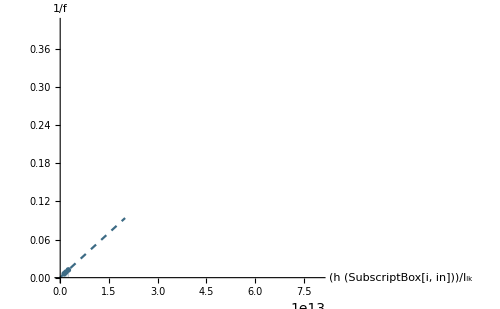
Current Fit Equation:  4.67046×10^-15 t+0.000417224
-Graphics-
ρ_tau:  4.67046×10^-15
Theoretical τ values:  {0.005,0.007,0.01}
Equivalent τ values:  {0.00702088,0.00988604,0.0142464}

```mathematica
bifiInRevDer=10;
bifMaxXRevDer=8*10^13;
bifMaxYRevDer=0.4;
bifIndexRevDer=Position[iInValsRevDer,bifiInRevDer]⟦1,1⟧;
plotValsRevDer⟦bifIndexRevDer⟧⟦1;;3⟧;
bifTauFitEqRevDer=Fit[plotValsRevDer⟦bifIndexRevDer⟧⟦1;;3⟧,{1,t},t];
bifTauFitRulesRevDer=FindFit[plotValsRevDer⟦bifIndexRevDer⟧⟦1;;3⟧,m t+b,{m,b},t];
bifEquivalentTauValsRevDer=m/IlkValuesRevDer⟦1;;3⟧/.bifTauFitRulesRevDer;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[bifTauFitEqRevDer,Italic]}]},
{Show[
ListLinePlot[plotValsRevDer⟦bifIndexRevDer⟧⟦1;;3⟧,PlotRange->{{0,bifMaxXRevDer},{0,bifMaxYRevDer}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦1⟧,ImageSize->imageSize],
ListPlot[plotValsRevDer⟦bifIndexRevDer⟧⟦1;;3⟧,PlotStyle->dataStyle⟦1⟧,ImageSize->imageSize, Filling->Axis, PlotMarkers->{Automatic,Medium},PlotRange->{{0,bifMaxXRevDer},{0,bifMaxYRevDer}}],
Plot[bifTauFitEqRevDer,{t,0,2*10^13},PlotStyle->dashedStyle⟦1⟧,ImageSize->imageSize]
]},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.bifTauFitRulesRevDer,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauValsRevDer⟦1;;3⟧,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[bifEquivalentTauValsRevDer,Italic]}]}
}]
```

## Original Derivation p_tau Calculator

### Ask user to select an input file with the τ data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/SomaTauMeas", WindowTitle->"Select Parsed Simulation Data File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/SomaTauMeas_OrigData

File Name: SomaSimTauData.txt

```mathematica
{tauVals, iInVals, data}=GetData[fileName];
(*i=Import[fileName,"Data"];
tauVals=Rest[i⟦1⟧];
iInVals =Rest[i⟦;;,1⟧];
data=i⟦2;;,2;;⟧;*)
Ilkbase=332.698*10^-15;
Ilkr=9.55616*10^-15;
IlkValues={Ilkbase/0.1,Ilkbase/0.2,Ilkbase/0.5,Ilkbase/1.0,Ilkbase/1.5,Ilkbase/2.0,Ilkbase/2.5};
IlkValues1={(Ilkbase+Ilkr(1-0.1))/0.1,(Ilkbase+Ilkr(1-0.2))/0.2,(Ilkbase+Ilkr(1-0.5))/0.5,(Ilkbase+Ilkr(1-1.0))/1.0,(Ilkbase+Ilkr(1-1.5))/1.5,(Ilkbase+Ilkr(1-2.0))/2.0,(Ilkbase+Ilkr(1-2.5))/2.5};
Print[Style["τ values: ", FontFamily->"Helvetica", Bold],tauVals];
Print[Style["I_lk values(A): (assuming Ilk= ", FontFamily->"Helvetica", Bold],
Ilkbase,
Style[" when τ=0.01s)", FontFamily->"Helvetica", Bold],
IlkValues];
Print[Style["ι_in values: ", FontFamily->"Helvetica", Bold],iInVals];
Print[Style["Raw Data Firing Rates: ", FontFamily->"Helvetica", Bold],data];
xValues=Transpose[h[#]&/@iInVals/#&/@IlkValues];
xValues1=Transpose[h[#]&/@iInVals/#&/@IlkValues1];
firingRatePlotVals=1/data;
plotVals=Transpose[{Take[xValues⟦#⟧,Length[firingRatePlotVals⟦#⟧]],firingRatePlotVals⟦#⟧}]&/@Range[Length[xValues]];
plotVals1=Transpose[{Take[xValues1⟦#⟧,Length[firingRatePlotVals⟦#⟧]],firingRatePlotVals⟦#⟧}]&/@Range[Length[xValues1]];
Print[Style["Plot Data: ", FontFamily->"Helvetica", Bold],plotVals];
```

τ values: {0.001,0.002,0.005,0.01,0.015,0.02,0.025}

I_lk values(A): (assuming Ilk= 3.32698×10^-13 when τ=0.01s){3.32698×10^-12,1.66349×10^-12,6.65396×10^-13,3.32698×10^-13,2.21799×10^-13,1.66349×10^-13,1.33079×10^-13}

ι_in values: {9999,10,15,20,25,30,40,50,55,75,100,200}

Raw Data Firing Rates: (3.32698×10^-12 | 1.66349×10^-12 | 6.65396×10^-13 | 3.32698×10^-13 | 2.21799×10^-13 | 1.66349×10^-13 | 1.33079×10^-13
675.19 | 344.83 | 141.24 | 71.612 | 47.996 | 36.087 | 28.892
821.04 | 418.32 | 171.29 | 86.912 | 58.271 | 43.899 | 35.195
938.42 | 477.74 | 195.33 | 99.108 | 66.59 | 50.121 | 40.199
1039.2 | 527.77 | 215.55 | 109.4 | 73.457 | 55.333 | 44.414
1127.3 | 571.5 | 233.29 | 118.38 | 79.498 | 59.941 | 48.092
1279.6 | 646.88 | 263.42 | 133.57 | 89.767 | 67.683 | 54.329
1410.8 | 711.32 | 288.91 | 146.34 | 98.359 | 74.16 | 59.553
1470.5 | 740.52 | 300.49 | 152.08 | 102.17 | 77.009 | 61.855
1680.9 | 842.55 | 340.33 | 172.05 | 115.54 | 87.074 | 69.948
1902.3 | 948.39 | 381.41 | 192.51 | 129.18 | 97.315 | 78.196
2574.2 | 1264.2 | 500.92 | 251.58 | 168.35 | 126.57 | 101.64)

Plot Data: ({6.70761×10^9,3.00573×10^11} | {1.34152×10^10,6.01146×10^11} | {3.35381×10^10,1.50286×10^12} | {6.70761×10^10,3.00573×10^12} | {1.00614×10^11,4.50859×10^12} | {1.34152×10^11,6.01146×10^12} | {1.6769×10^11,7.51433×10^12}
{2.47733×10^11,0.00148106} | {4.95466×10^11,0.00289998} | {1.23867×10^12,0.00708015} | {2.47733×10^12,0.0139641} | {3.716×10^12,0.0208351} | {4.95466×10^12,0.0277108} | {6.19333×10^12,0.0346117}
{1.95844×10^11,0.00121797} | {3.91687×10^11,0.00239051} | {9.79218×10^11,0.00583805} | {1.95844×10^12,0.0115059} | {2.93765×10^12,0.0171612} | {3.91687×10^12,0.0227796} | {4.89609×10^12,0.0284131}
{1.6649×10^11,0.00106562} | {3.32979×10^11,0.00209319} | {8.32448×10^11,0.00511954} | {1.6649×10^12,0.01009} | {2.49735×10^12,0.0150173} | {3.32979×10^12,0.0199517} | {4.16224×10^12,0.0248762}
{1.47083×10^11,0.000962279} | {2.94165×10^11,0.00189476} | {7.35413×10^11,0.00463929} | {1.47083×10^12,0.00914077} | {2.20624×10^12,0.0136134} | {2.94165×10^12,0.0180724} | {3.67707×10^12,0.0225154}
{1.33066×10^11,0.000887075} | {2.66133×10^11,0.00174978} | {6.65332×10^11,0.00428651} | {1.33066×10^12,0.00844737} | {1.996×10^12,0.0125789} | {2.66133×10^12,0.0166831} | {3.32666×10^12,0.0207935}
{1.13817×10^11,0.000781494} | {2.27634×10^11,0.00154588} | {5.69086×10^11,0.00379622} | {1.13817×10^12,0.00748671} | {1.70726×10^12,0.01114} | {2.27634×10^12,0.0147748} | {2.84543×10^12,0.0184064}
{1.00955×10^11,0.000708818} | {2.01911×10^11,0.00140584} | {5.04777×10^11,0.00346129} | {1.00955×10^12,0.0068334} | {1.51433×10^12,0.0101668} | {2.01911×10^12,0.0134844} | {2.52388×10^12,0.0167918}
{9.59437×10^10,0.000680041} | {1.91887×10^11,0.0013504} | {4.79719×10^11,0.0033279} | {9.59437×10^11,0.00657549} | {1.43916×10^12,0.00978761} | {1.91887×10^12,0.0129855} | {2.39859×10^12,0.0161668}
{8.13838×10^10,0.000594919} | {1.62768×10^11,0.00118687} | {4.06919×10^11,0.00293832} | {8.13838×10^11,0.00581226} | {1.22076×10^12,0.00865501} | {1.62768×10^12,0.0114845} | {2.03459×10^12,0.0142963}
{6.99539×10^10,0.000525679} | {1.39908×10^11,0.00105442} | {3.49769×10^11,0.00262185} | {6.99539×10^11,0.00519454} | {1.04931×10^12,0.00774114} | {1.39908×10^12,0.0102759} | {1.74885×10^12,0.0127884}
{4.87784×10^10,0.00038847} | {9.75568×10^10,0.000791014} | {2.43892×10^11,0.00199633} | {4.87784×10^11,0.00397488} | {7.31676×10^11,0.00594001} | {9.75568×10^11,0.00790077} | {1.21946×10^12,0.00983865})

### Fit Data to a Linear Model

```mathematica
fitLineEq=Fit[#,{1,t},t]&/@plotVals
fitLineRules=FindFit[#,m t+b,{m,b},t]&/@plotVals;
fitLineEq1=Fit[#,{1,t},t]&/@plotVals1
fitLineRules1=FindFit[#,m t+b,{m,b},t]&/@plotVals1;
```

{44.8107 t-2.19797×10^6,5.56617×10^-15 t+0.000146679,5.7818×10^-15 t+0.00014067,5.95428×10^-15 t+0.000127156,6.10274×10^-15 t+0.000117851,6.22909×10^-15 t+0.00011049,6.44868×10^-15 t+0.0000973845,6.63553×10^-15 t+0.0000858177,6.72449×10^-15 t+0.0000786145,7.01451×10^-15 t+0.000062934,7.30542×10^-15 t+0.0000486566,8.07612×10^-15 t+0.0000146854}

{42.8827 t+7.03556×10^10,5.32654×10^-15 t+0.000469826,5.53269×10^-15 t+0.000406491,5.69771×10^-15 t+0.000359932,5.83968×10^-15 t+0.000328777,5.96054×10^-15 t+0.000305319,6.1706×10^-15 t+0.000269994,6.34934×10^-15 t+0.000243418,6.43447×10^-15 t+0.000230394,6.71196×10^-15 t+0.000197257,6.9903×10^-15 t+0.000168913,7.72791×10^-15 t+0.000107299}

### Plot Data

```mathematica
Clear[currPlotNum];
Manipulate[
imageSize=500;
currPlotNum=Flatten[Position[iInVals,curriIn]]⟦1⟧;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[fitLineEq⟦currPlotNum⟧,Italic]}]},
{Show[
ListLinePlot[plotVals⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals,PlotStyle->dataStyle,ImageSize->imageSize],
Plot[fitLineEq⟦currPlotNum⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListLinePlot[plotVals1⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals1,PlotStyle->dataStyle,ImageSize->imageSize],
Plot[fitLineEq1⟦currPlotNum⟧,{t,0,maxX},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize]

]
},
{Show[
ListLinePlot[plotVals⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals⟦currPlotNum⟧,PlotStyle->Directive[dataStyle⟦currPlotNum⟧,PointSize[Large]],ImageSize->imageSize],
Plot[fitLineEq⟦currPlotNum⟧,{t,0,maxX},PlotStyle->dashedStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListLinePlot[plotVals1⟦currPlotNum⟧,PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize],
ListPlot[plotVals1⟦currPlotNum⟧,PlotStyle->Directive[dataStyle⟦currPlotNum⟧,PointSize[Large]],ImageSize->imageSize],
Plot[fitLineEq1⟦currPlotNum⟧,{t,0,maxX},PlotStyle->boldStyle⟦currPlotNum⟧,ImageSize->imageSize]
]
},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.fitLineRules⟦currPlotNum⟧,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauVals,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[m/IlkValues/.fitLineRules⟦currPlotNum⟧,Italic]}]}
}],
{{curriIn,iInVals⟦Position[iInVals,Max[iInVals]]⟦1,1⟧⟧,"i_in"},Reverse[iInVals]},
{{maxX,1.*10^13,"Max X-axis value"},1*10^12,10*10^13,5*10^11, Appearance-> "Open"},
{{maxY,0.05,"Max Y-axis value"},0.01, 1,0.005, Appearance-> "Open"},
LabelStyle->Medium
]
```

### Determine if τ is accurate when ι_in is near bifurcation

```mathematica
iInVals
```

{0.51,0.6,1,5,100,10,15,200,20,25,30,400,40,50,55,75}

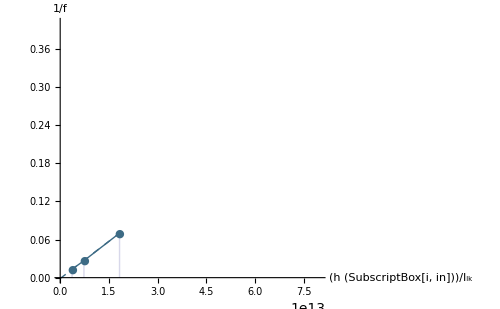
Current Fit Equation:  3.89768×10^-15 t-0.00135689
-Graphics-
ρ_tau:  3.89768×10^-15
Theoretical τ values:  {0.001,0.002,0.005}
Equivalent τ values:  {0.00117154,0.00234307,0.00585768}

```mathematica
bifiIn=0.6;
bifMaxX=8*10^13;
bifMaxY=0.4;
bifIndex=Position[iInVals,bifiIn]⟦1,1⟧;
plotVals⟦bifIndex⟧⟦1;;3⟧;
bifTauFitEq=Fit[plotVals⟦bifIndex⟧⟦1;;3⟧,{1,t},t];
bifTauFitRules=FindFit[plotVals⟦bifIndex⟧⟦1;;3⟧,m t+b,{m,b},t];
bifEquivalentTauVals=m/IlkValues⟦1;;3⟧/.bifTauFitRules;
Grid[{
{Row[{Style["Current Fit Equation:  ",FontFamily->"Helvetica", Bold] ,Style[bifTauFitEq,Italic]}]},
{Show[
ListLinePlot[plotVals⟦bifIndex⟧⟦1;;3⟧,PlotRange->{{0,bifMaxX},{0,bifMaxY}},AxesLabel->{"(h (SubscriptBox[i, in]))/I_lk","1/f"},PlotStyle->boldStyle⟦1⟧,ImageSize->imageSize],
ListPlot[plotVals⟦bifIndex⟧⟦1;;3⟧,PlotStyle->dataStyle⟦1⟧,ImageSize->imageSize, Filling->Axis, PlotMarkers->{Automatic,Medium},PlotRange->{{0,bifMaxX},{0,bifMaxY}}],
Plot[bifTauFitEq,{t,0,2*10^13},PlotStyle->dashedStyle⟦1⟧,ImageSize->imageSize]
]},
{Row[{Style["ρ_tau:  ",FontFamily->"Helvetica", Bold] ,Style[m/.bifTauFitRules,Italic]}]},
{Row[{Style["Theoretical τ values:  ",FontFamily->"Helvetica", Bold] ,Style[tauVals⟦1;;3⟧,Italic]}]},
{Row[{Style["Equivalent τ values:  ",FontFamily->"Helvetica", Bold] ,Style[bifEquivalentTauVals,Italic]}]}
}]
```

## Appendix

### Color Chooser

Vary the index value of ColorData and see new colors appear.  These values once set change the colors used in the plot.

```mathematica
dataStyle=Reverse[Join[ColorData[90,"ColorList"],ColorData[31,"ColorList"]]];
dashedStyle=Tuples[{{Dashed}, dataStyle}];
boldStyle=Tuples[{{Thick}, dataStyle}];
Graphics[{#,PointSize[1],Point[{0,0}]},ImageSize-> 30]&/@dataStyle
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Input and Organize data

```mathematica
(*tauFiringRatesRawData=({{f, 5, 15, 25, 55}, {.001, 472.31, 820.09, 1039.2, 1470.5}, {.002, 241.17, 418.33, 527.77, 740.52}, {.005, 98.64, 171.29, 215.55, 300.49}, {.010, 49.81, 86.92, 109.4, 152.08}, {.015, 33.27, 58.27, 73.46, 102.17}, {.020, 24.92, 43.90, 55.33, 77.01}, {.025, 19.89, 35.19, 44.41, 61.88}});
iInValues=Rest[tauFiringRatesRawData⟦1⟧];
tauValues=Rest[Transpose[tauFiringRatesRawData]⟦1⟧];
Ilkbase=332.698*10^-15;
IlkValues={Ilkbase/0.1,Ilkbase/0.2,Ilkbase/0.5,Ilkbase/1.0,Ilkbase/1.5,Ilkbase/2.0,Ilkbase/2.5};
xValues=Transpose[h[#]&/@iInValues/#&/@IlkValues];
firingRatePlotVals=Transpose[1/Transpose[Rest[Transpose[Rest[tauFiringRatesRawData]]]]];
plotVals1=Transpose[{xValues⟦#⟧,firingRatePlotVals⟦#⟧}]&/@Range[Length[xValues]]
fitLineEq=Fit[#,{1,t},t]&/@plotVals1
fitLineRules=FindFit[#,m t+b,{m,b},t]&/@plotVals1*)
```